Transformation Matrix:  (1 | 2
3 | 4)

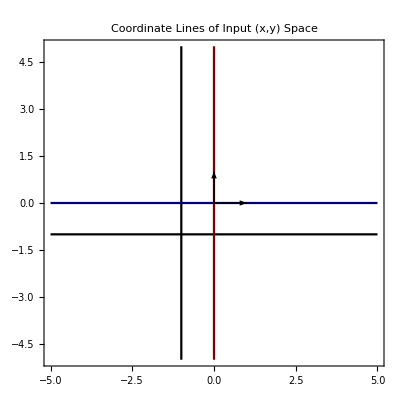

Basis Vectors:  {(1
0),(0
1)}

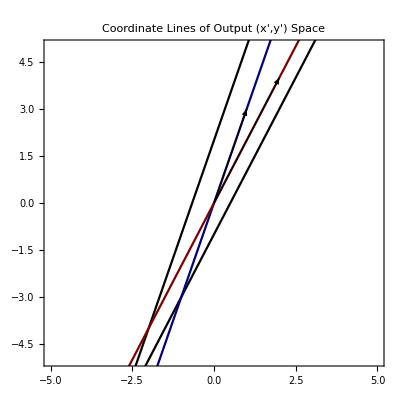

Section 1) Basic Facts about the Transformation

Basis Vectors:  {(1
3),(2
4)}

Determinant:  -2

Jacobian:  (1 | 2
3 | 4)

Unit Basis Vectors:  {(1/(√10)
3/(√10)),(√(2/5)
2 √(2/5))}

Section 2) Unique Vectors Under Transform

Null Space (Vectors that become 0 vectors upon being transformed):  {}

Eigenvectors (Vectors that get scaled up or down upon being transformed):  {{1/6 (-3+√33),1},{1/6 (-3-√33),1}}

Corresponding Eigenvalues: {1/2 (5+√33),1/2 (5-√33)}

```mathematica
T= {{1, 2}, {3,4}};
Text["Transformation Matrix: "]Text[T // MatrixForm]
n = 1;
BaseColor= 1/(2*n);
func ={};
For[i =-n, i< n, i++,
plotx = ParametricPlot[{{x, i}}, {x, -5, 5}, PlotStyle->{RGBColor[0,0, BaseColor * (i+n)]}, PlotRange -> {{-5, 5}, {-5,5}}, PlotLabel ->  Style["Coordinate Lines of Input (x,y) Space", FontSize -> 14, FontColor -> Black], Frame -> True];
ploty = ParametricPlot[{i, y}, {y, -5, 5},PlotStyle->{RGBColor[BaseColor * (i+n),0,0]}, PlotRange -> {{-5, 5}, {-5,5}}];
AppendTo[func, {plotx, ploty}];
]
basisVectors = Graphics[{Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{0,1}}]},Axes->True];
AppendTo[func, basisVectors];
Show[func]

Text["Basis Vectors: "]Text[ {{1,0} // MatrixForm, {0,1} // MatrixForm} ]

funcT = {};
For[i =-n, i< n, i++,
plotx = ParametricPlot[{T.{x, i}}, {x, -7, 7}, PlotStyle->{RGBColor[0,0, BaseColor * (i+n)]}, PlotRange -> {{-5, 5}, {-5,5}}, PlotLabel -> Style["Coordinate Lines of Output (x',y') Space", FontSize -> 14, FontColor -> Black], Frame -> True];
ploty = ParametricPlot[T.{i, y}, {y, -7, 7},PlotStyle->{RGBColor[BaseColor * (i+n),0,0]}, PlotRange -> {{-5, 5}, {-5,5}}];
AppendTo[funcT, {plotx, ploty}]
]
basisVectorsT = Graphics[{Arrow[{T.{0,0},T.{1,0}}],Arrow[{T.{0,0},T.{0,1}}]},Axes->True];
AppendTo[funcT, basisVectorsT];
Show[funcT]

Style["Section 1) Basic Facts about the Transformation", Bold, FontSize -> 20]
Text["Basis Vectors: "]Text[ {T.{1,0} // MatrixForm, T.{0,1} // MatrixForm} ]
Text["Determinant: "]Text[Det[T] // MatrixForm]
Text["Jacobian: "] Text[T//MatrixForm]
UB1 = T.{1,0}/Sqrt[(T.{1,0}).(T.{1,0})];
UB2 = T.{0,1}/Sqrt[(T.{1,0}).(T.{1,0})];
Text ["Unit Basis Vectors: "] Text[ {UB1 // MatrixForm, UB2 // MatrixForm} ]

Style["Section 2) Unique Vectors Under Transform", Bold, FontSize -> 20]
Text ["Null Space (Vectors that become 0 vectors upon being transformed): "] Text[NullSpace[T]//MatrixForm]
Text ["Eigenvectors (Vectors that get scaled up or down upon being transformed): "] Text[Eigenvectors[T]]
Text["Corresponding Eigenvalues:"] Text[Eigenvalues[T]]
```